```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
min= -100;  max= 1; step=0.025;
```

```mathematica
Subscript[Ω, m0]=0.315;  H0.b2=(67.37)^2; Subscript[Ω, Λ0]= 0.6847; Subscript[Ω, r0]= 3 10^(-4);
```

```mathematica
β=0.45; α=0.93; title="β=0.45   α=0.93";
```

```mathematica
Subscript[Δ, 1]=0.0; Subscript[Δ, 2]=3 10^-3; Subscript[Δ, 3]=7 10^-3; Subscript[Δ, 4]=1 10^-2; Subscript[Δ, 5]=2 10^-2;     legends={"Δ= 0","Δ= 3 x10^-3","Δ= 7 x10^-3","Δ= 10 x10^-3","Δ= 20 x10^-3","ΛCDM"};
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
HΛCDM[x_]:= Sqrt[H0.b2(Subscript[Ω, m0] Exp[-3x]+ Subscript[Ω, r0] Exp[-4x] + Subscript[Ω, Λ0])];
```

```mathematica
Friedmann= (β/2) y'[x] + α y[x]  - (  y[x] -Subscript[Ω, m0] H0.b2 Exp[-3x] -Subscript[Ω, r0] H0.b2 Exp[-4x]  )^(2/(2-Δ)) ==0
```

0.93 y[x]-(-1.36162 ⅇ^(-4 x)-1429.7 ⅇ^(-3 x)+y[x])^(2/(2-Δ))+0.225 y'[x]==0

```mathematica
Solucion1=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ-> Subscript[Δ, 1] } ,y[x],{x,min,max},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10];
```

```mathematica
Solucion2=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ->Subscript[Δ, 2]} ,y[x],{x,min,max},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10];
```

```mathematica
Solucion3=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ->Subscript[Δ, 3]} ,y[x],{x,min,max},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10];
```

```mathematica
Solucion4=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ->Subscript[Δ, 4]} ,y[x],{x,min,max},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10];
```

```mathematica
Solucion5=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ->Subscript[Δ, 5]} ,y[x],{x,min,max},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10];
```

```mathematica
X= Range[min,max,step];   H2=Solucion1[[0]];  H22=Solucion2[[0]]; H23=Solucion3[[0]]; H24=Solucion4[[0]]; H25=Solucion5[[0]];
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
dH2dx= ND[H2[x],x,X,WorkingPrecision->40,Terms->12];  dH22dx= ND[H22[x],x,X,WorkingPrecision->40,Terms->12];  dH23dx= ND[H23[x],x,X,WorkingPrecision->40,Terms->12];  dH24dx= ND[H24[x],x,X,WorkingPrecision->40,Terms->12]; dH25dx= ND[H25[x],x,X,WorkingPrecision->40,Terms->12];
```

InterpolatingFunction::dmval: Input value {1.025} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.075} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
rhoL= 3 (α H2[X]+ (β/2) dH2dx)^(1-(Δ/2)) /. {Δ-> 0.0}; rhoL2= 3 (α H22[X]+ (β/2) dH22dx)^(1-(Δ/2)) /. {Δ-> 7 10^-3}; rhoL3= 3 (α H23[X]+ (β/2) dH23dx)^(1-(Δ/2)) /. {Δ-> 14 10^-3};
```

```mathematica
rhom= 3 Subscript[Ω, m0] H0.b2 Exp[-3X]; rhor= 3 Subscript[Ω, r0] H0.b2 Exp[-4X];
```

```mathematica
styles={Directive[Line,Lighter[Black]],Directive[DotDashed],Directive[Dashing[{0.02}]],Directive[Dashed,Orange],Directive[Line,Lighter[Blue]]};
```

```mathematica
ListLinePlot[{Transpose[{X,Log[rhoL]}],Transpose[{X,Log[rhoL2]}],Transpose[{X,Log[rhoL3]}],Transpose[{X,Log[rhom]}],Transpose[{X,Log[rhor]}]}, PlotRange->{{Automatic,Automatic},{-200,280}},ImageSize->Large,Frame->True,PlotStyle-> styles,PlotLegends-> Placed[{"DE Δ= 0","DE Δ=  7 x10^-3","DE Δ=  14 x10^-3","Materia","Radiación"},{0.85,0.8}], FrameLabel->{{"ln(ρ)",""},{"x = -Ln(1+z)",title}},LabelStyle->Directive[Black,Bold,10]]
```

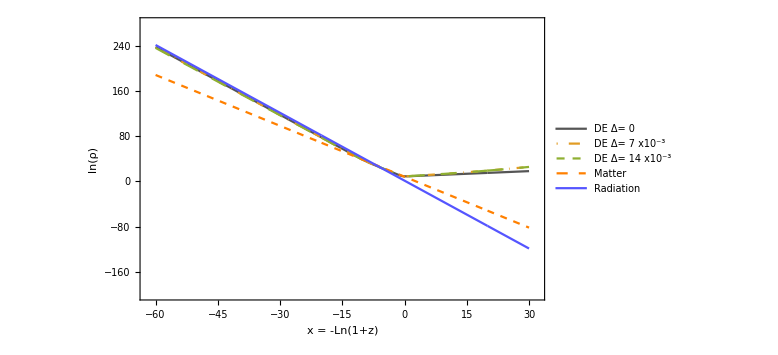

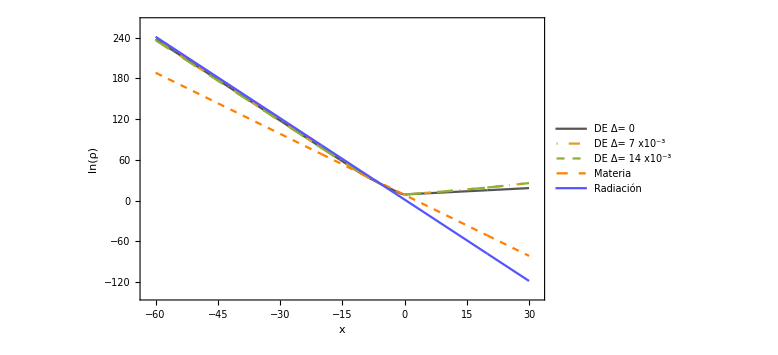

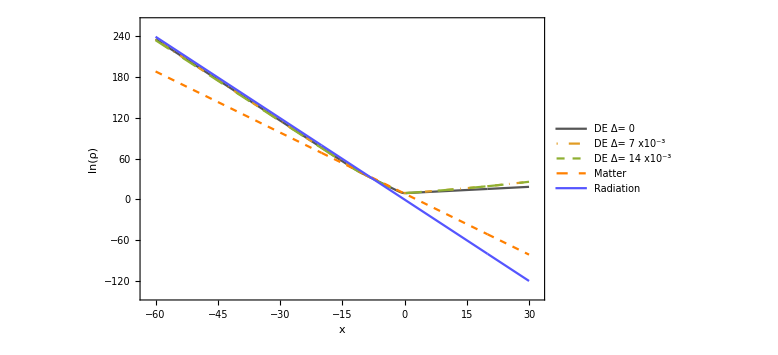

-Graphics-

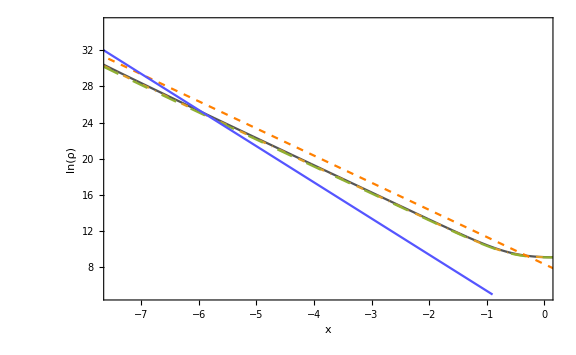

```mathematica
ListLinePlot[{Transpose[{X,Log[rhoL]}],Transpose[{X,Log[rhoL2]}],Transpose[{X,Log[rhoL3]}],Transpose[{X,Log[rhom]}],Transpose[{X,Log[rhor]}]}, PlotRange->{{-7.5,0},{5,35}},ImageSize->Large,Frame->True,PlotStyle-> styles, FrameLabel->{{"ln(ρ)",""},{"x",""}},LabelStyle->Directive[Black,Bold,8]]
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
Subscript[ρ̃, Λ1]= (1/H0.b2)(α H2[X]+ (β/2) dH2dx)^(1-(Δ/2)) /. {Δ-> Subscript[Δ, 1]}; dataZvsDE1= Transpose[{X,Subscript[ρ̃, Λ1]}];
```

```mathematica
Subscript[ρ̃, Λ2]= (1/H0.b2)(α H22[X]+ (β/2) dH22dx)^(1-(Δ/2)) /. {Δ-> Subscript[Δ, 2]}; dataZvsDE2= Transpose[{X,Subscript[ρ̃, Λ2]}];
```

```mathematica
Subscript[ρ̃, Λ3]= (1/H0.b2)(α H23[X]+ (β/2) dH23dx)^(1-(Δ/2)) /. {Δ-> Subscript[Δ, 3]}; dataZvsDE3= Transpose[{X,Subscript[ρ̃, Λ3]}];
```

```mathematica
Subscript[ρ̃, Λ4]= (1/H0.b2)(α H24[X]+ (β/2) dH24dx)^(1-(Δ/2)) /. {Δ-> Subscript[Δ, 4]}; dataZvsDE4= Transpose[{X,Subscript[ρ̃, Λ4]}];
```

```mathematica
Subscript[ρ̃, Λ5]= (1/H0.b2)(α H25[X]+ (β/2) dH25dx)^(1-(Δ/2)) /. {Δ-> Subscript[Δ, 5]}; dataZvsDE5= Transpose[{X,Subscript[ρ̃, Λ5]}];
```

```mathematica
Subscript[ρ̃, c1]= (1/H0.b2)*H2[X] ;
```

```mathematica
Subscript[ρ̃, c2]= (1/H0.b2)*H22[X] ;
```

```mathematica
Subscript[ρ̃, c3]= (1/H0.b2)*H23[X] ;
```

```mathematica
Subscript[ρ̃, c4]= (1/H0.b2)*H24[X] ;
```

```mathematica
Subscript[ρ̃, c5]= (1/H0.b2)*H25[X] ;
```

```mathematica
Subscript[ρ̃, cCDM]= (1/H0.b2)*(HΛCDM[X])^2 ;
```

```mathematica
Subscript[Ω, Λ1]= Subscript[ρ̃, Λ1]/Subscript[ρ̃, c1]; dataZvsODE1= Transpose[{-X,Subscript[Ω, Λ1]}];
```

```mathematica
Subscript[Ω, Λ2]= Subscript[ρ̃, Λ2]/Subscript[ρ̃, c2]; dataZvsODE2= Transpose[{-X,Subscript[Ω, Λ2]}];
```

```mathematica
Subscript[Ω, Λ3]= Subscript[ρ̃, Λ3]/Subscript[ρ̃, c3]; dataZvsODE3= Transpose[{-X,Subscript[Ω, Λ3]}];
```

```mathematica
Subscript[Ω, Λ4]= Subscript[ρ̃, Λ4]/Subscript[ρ̃, c4]; dataZvsODE4= Transpose[{-X,Subscript[Ω, Λ4]}];
```

```mathematica
Subscript[Ω, Λ5]= Subscript[ρ̃, Λ5]/Subscript[ρ̃, c5]; dataZvsODE5= Transpose[{-X,Subscript[Ω, Λ5]}];
```

```mathematica
Subscript[Ω, ΛCDM]= Subscript[Ω, Λ0]/Subscript[ρ̃, cCDM]; dataZvsODECDM= Transpose[{-X,Subscript[Ω, ΛCDM]}];
```

```mathematica
styles={Directive[Line],Directive[DotDashed],Directive[Dashing[{0.008}]],Directive[Line],Directive[DotDashed],Directive[Dashing[{0.008}],Black,Thickness[0.004]]};
```

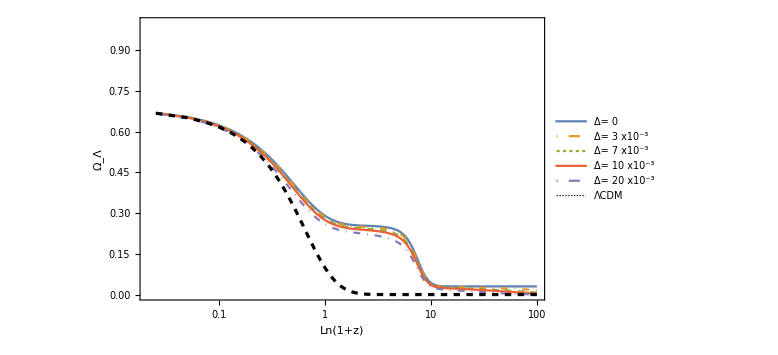

```mathematica
ListLinePlot[{dataZvsODE1,dataZvsODE2,dataZvsODE3,dataZvsODE4,dataZvsODE5,dataZvsODECDM},PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,PlotLegends-> legends,PlotRange->{{Automatic,Automatic},{0.0,1}},ScalingFunctions->{"Log"},Frame->True, FrameLabel->{{"Ω_Λ",""},{"Ln(1+z)",title}}]
```

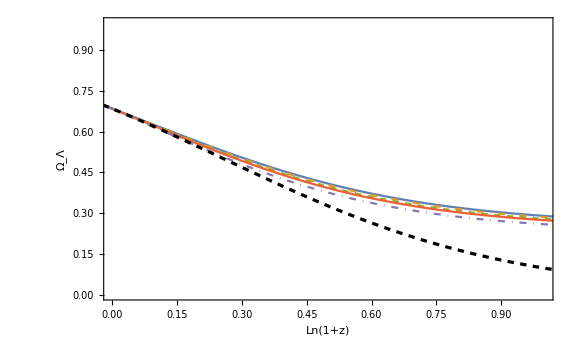

```mathematica
ListLinePlot[{dataZvsODE1,dataZvsODE2,dataZvsODE3,dataZvsODE4,dataZvsODE5,dataZvsODECDM},PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,PlotRange->{{0.0,1},{0,1}},Frame->True, FrameLabel->{{"Ω_Λ",""},{"Ln(1+z)",title}}]
```

```mathematica
DEz1=Interpolation[dataZvsDE1,Method->"Hermite"];
```

```mathematica
DEz2=Interpolation[dataZvsDE2,Method->"Hermite"];
```

```mathematica
DEz3=Interpolation[dataZvsDE3,Method->"Hermite"];
```

```mathematica
DEz4=Interpolation[dataZvsDE4,Method->"Hermite"];
```

```mathematica
DEz5=Interpolation[dataZvsDE5,Method->"Hermite"];
```

```mathematica
Subscript[P̃, Λ1]=-Subscript[ρ̃, Λ1]- (1/3) ND[DEz1[x],x,X,WorkingPrecision->40,Terms->12]; dataZvsPDE1= Transpose[{X,Subscript[P̃, Λ1]}];
```

```mathematica
Subscript[P̃, Λ2]=-Subscript[ρ̃, Λ2]- (1/3) ND[DEz2[x],x,X,WorkingPrecision->40,Terms->12]; dataZvsPDE2= Transpose[{X,Subscript[P̃, Λ2]}];
```

```mathematica
Subscript[P̃, Λ3]=-Subscript[ρ̃, Λ3]- (1/3) ND[DEz3[x],x,X,WorkingPrecision->40,Terms->12]; dataZvsPDE3= Transpose[{X,Subscript[P̃, Λ3]}];
```

```mathematica
Subscript[P̃, Λ4]=-Subscript[ρ̃, Λ4]- (1/3) ND[DEz4[x],x,X,WorkingPrecision->40,Terms->12]; dataZvsPDE4= Transpose[{X,Subscript[P̃, Λ4]}];
```

```mathematica
Subscript[P̃, Λ5]=-Subscript[ρ̃, Λ5]- (1/3) ND[DEz5[x],x,X,WorkingPrecision->40,Terms->12]; dataZvsPDE5= Transpose[{X,Subscript[P̃, Λ5]}];
```

```mathematica
Subscript[w, Λ1]=Subscript[P̃, Λ1] /Subscript[ρ̃, Λ1]; dataZvsWDE1= Transpose[{-X,Subscript[w, Λ1]}];
```

```mathematica
Subscript[w, Λ2]=Subscript[P̃, Λ2] /Subscript[ρ̃, Λ2]; dataZvsWDE2= Transpose[{-X,Subscript[w, Λ2]}];
```

```mathematica
Subscript[w, Λ3]=Subscript[P̃, Λ3] /Subscript[ρ̃, Λ3]; dataZvsWDE3= Transpose[{-X,Subscript[w, Λ3]}];
```

```mathematica
Subscript[w, Λ4]=Subscript[P̃, Λ4] /Subscript[ρ̃, Λ4]; dataZvsWDE4= Transpose[{-X,Subscript[w, Λ4]}];
```

```mathematica
Subscript[w, Λ5]=Subscript[P̃, Λ5] /Subscript[ρ̃, Λ5]; dataZvsWDE5= Transpose[{-X,Subscript[w, Λ5]}];
```

```mathematica
Subscript[w, m][x_]:= N[1/3(1+x-x)]; dataZvsWm= Transpose[{-X,Subscript[w, m][X]}];
```

```mathematica
legends={"Δ= 0","Δ= 3 x10^-3","Δ= 7 x10^-3","Δ= 10 x10^-3","Δ= 20 x10^-3","w_rad= 1/3"};
```

```mathematica
styles={Directive[Line],Directive[DotDashed],Directive[Dashing[{0.008}]],Directive[Line],Directive[DotDashed],Directive[Dashing[{0.008}],Black,Thickness[0.004]]};
```

```mathematica
ListLinePlot[{dataZvsWDE1,dataZvsWDE2,dataZvsWDE3,dataZvsWDE4,dataZvsWDE5,dataZvsWm},PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,PlotLegends-> Placed[legends,{0.225,0.3}],Frame->True, FrameLabel->{{"w_Λ",""},{"Ln(1+z)",title}},PlotRange->{{-1,20},{-1.2,0.4}}]
```

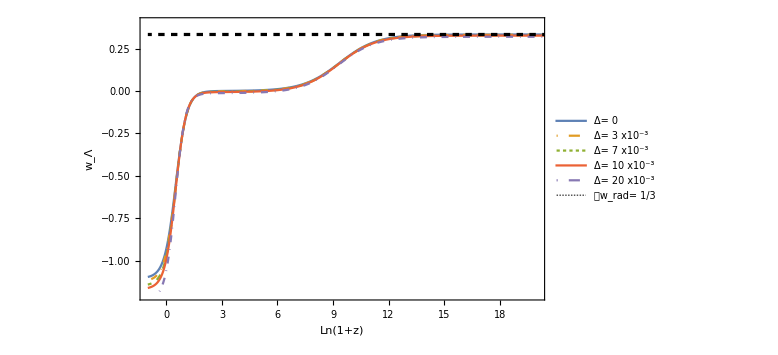

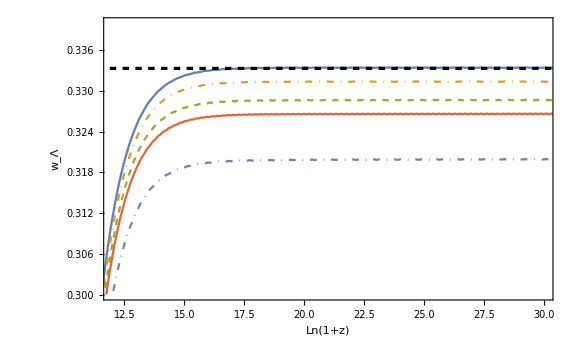

```mathematica
ListLinePlot[{dataZvsWDE1,dataZvsWDE2,dataZvsWDE3,dataZvsWDE4,dataZvsWDE5,dataZvsWm},PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"w_Λ",""},{"Ln(1+z)",""}},PlotRange->{{12,30},{0.3,0.34}}]
```